```mathematica
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2meV=1000*8.617332478*10^−5;K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)

(*define sigma and kappa kernels*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(energy^2)*D[fermiDirac[energy,temp],energy]
```

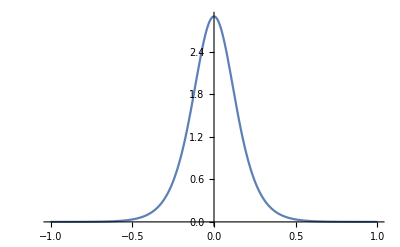

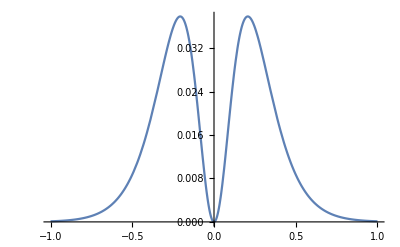

```mathematica
(*Plot Kernel for charge transport (sigma) and heat flux (kappa)*)
B=1;
Plot[Evaluate[sigmaK[energy,1000]],{energy,-B,B},PlotRange->All]
Plot[Evaluate[kappaK[energy,1000]],{energy,-B,B},PlotRange->All]
```

{√Abs[energy],Abs[energy],Abs[energy]^2}

{√Abs[energy]+Ramp[2 energy],Abs[energy]+Ramp[2 energy],Abs[energy]^2+Ramp[2 energy]}

{√Abs[energy]+Ramp[-2 energy],Abs[energy]+Ramp[-2 energy],Abs[energy]^2+Ramp[-2 energy]}

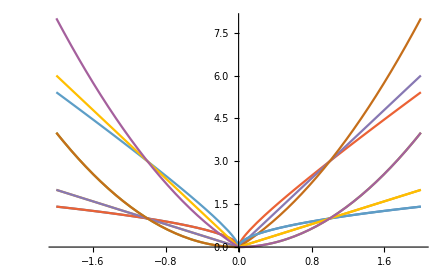

```mathematica
symDOS={Abs[energy^(1/2)],Abs[energy],Abs[energy^2]}
largeValDOS=symDOS+Ramp[2energy]
largeCondDOS=symDOS+Ramp[-2energy]
Plot[{symDOS,Evaluate@largeValDOS,Evaluate@largeCondDOS},{energy,-2,2}]
```

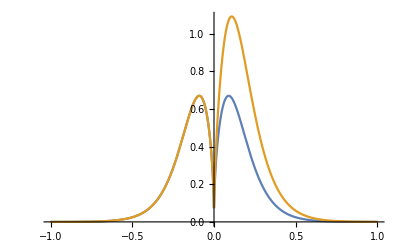

```mathematica
Plot[{Evaluate[symDOS[[1]]*sigmaK[energy,1000]],Evaluate[largeValDOS[[1]]*sigmaK[energy,1000]],largeValDOS},{energy,-B,B},PlotRange->All]
```

```mathematica
Plot[]
```

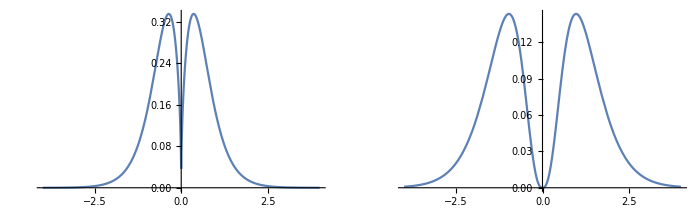

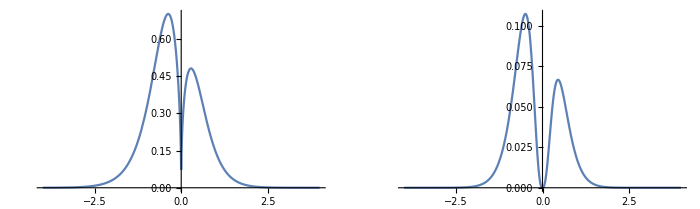

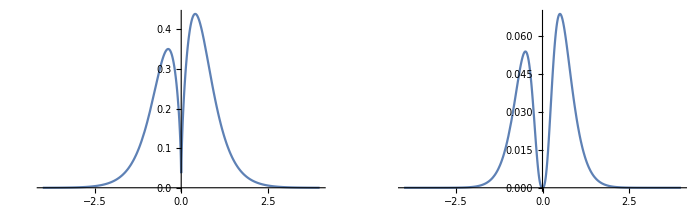

```mathematica
(*electron charge transport kernel times symmetric DoS*)(*electron  heat flux kernel times symmetric DoS*)
GraphicsGrid[{{Plot[Evaluate[-Abs[Sqrt[ee]]*DfermiDirac[ee,4000]],{ee,-4,4},PlotRange->All],Plot[Evaluate[-Abs[Sqrt[ee]]*ee*ee*DfermiDirac[ee,4000]],{ee,-4,4},PlotRange->All]}}]
(*Smaller Valance band DOS - electron charge transport kernel times asymmetric DoS*)(*electron  heat flux kernel times asymmetric DoS*)
GraphicsGrid[{{Plot[Evaluate[-Abs[ee-2Sqrt[ee]]*DfermiDirac[ee,4000]],{ee,-4,4},PlotRange->All],Plot[Evaluate[-Abs[ee-2Sqrt[ee]]*ee*ee*DfermiDirac[ee,2000]],{ee,-4,4},PlotRange->All]}},ImageSize->700]
(*Smaller conduction band DOS - electron charge transport kernel times asymmetric DoS*)(*electron  heat flux kernel times asymmetric DoS*)
GraphicsGrid[{{Plot[Evaluate[-Abs[0.5ee+1Sqrt[ee]]*DfermiDirac[ee,4000]],{ee,-4,4},PlotRange->All],Plot[Evaluate[-Abs[0.5ee+1Sqrt[ee]]*ee*ee*DfermiDirac[ee,2000]],{ee,-4,4},PlotRange->All]}},ImageSize->700]
```

```mathematica
(*electron charge transport kernel times asymmetric DoS integrated over energy, across ten temperatures*)
(*Smaller conduction band DOS*)
chargeAsymm1=Table[NIntegrate[Evaluate[-Abs[ee-2Sqrt[ee]]*DfermiDirac[ee,T]],{ee,-4,4}]//N,{T,100,4000,100}]
(*Smaller valence band DOS*)
chargeAsymm2=Table[NIntegrate[Evaluate[-Abs[0.5ee+Sqrt[ee]]*DfermiDirac[ee,T]],{ee,-4,4}]//N,{T,100,4000,100}]
(*electron heat flux kernel times asymmetric DoS integrated over energy, across ten temperatures*)
heatAsymm1=Table[(1/T)*NIntegrate[Evaluate[-Abs[ee-Sqrt[ee]]*ee*ee*DfermiDirac[ee,T]],{ee,-4,4}]//N,{T,100,4000,100}]
heatAsymm2=Table[(1/T)*NIntegrate[Evaluate[-Abs[0.5ee+Sqrt[ee]]*ee*ee*DfermiDirac[ee,T]],{ee,-4,4}]//N,{T,100,4000,100}]
(*electron charge transport kernel times symmetric DoS integrated over energy, across ten temperatures*)
chargesymm=Table[NIntegrate[Evaluate[-Abs[Sqrt[ee]]*DfermiDirac[ee,T]],{ee,-4,4}]//N,{T,100,4000,100}]
(*electron heat flux kernel times symmetric DoS integrated over energy, across ten temperatures*)
heatsymm=Table[(1/T)*NIntegrate[Evaluate[-Abs[Sqrt[ee]]*ee*ee*DfermiDirac[ee,T]],{ee,-4,4}]//N,{T,100,4000,100}]
temmps=Table[T,{T,100,4000,100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.193293 and 0.000134723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.270138 and 0.0000674665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.32791 and 0.0000450225 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.193293,0.270138,0.32791,0.375838,0.417495,0.45471,0.488569,0.519778,0.548829,0.576077,0.601791,0.62618,0.64941,0.671614,0.692904,0.713372,0.733095,0.752141,0.770566,0.78842,0.805747,0.822586,0.83897,0.854929,0.870492,0.885682,0.900522,0.915031,0.929228,0.943129,0.95675,0.970105,0.983206,0.996065,1.00869,1.0211,1.03329,1.04529,1.05708,1.06869}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.10262 and 0.0000673618 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.147015 and 0.0000337336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.181874 and 0.0000225151 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.10262,0.147015,0.181874,0.211811,0.238613,0.263193,0.286096,0.307674,0.328172,0.347769,0.366599,0.384767,0.402355,0.41943,0.436048,0.452255,0.46809,0.483586,0.498771,0.513672,0.528308,0.542701,0.556866,0.570819,0.584573,0.598141,0.611534,0.624761,0.637833,0.650756,0.663539,0.676189,0.688711,0.701112,0.713397,0.72557,0.737636,0.749599,0.761462,0.773228}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {-0.000124333}. NIntegrate obtained 0.0000365894 and 4.45333×10^-11 for the integral and error estimates.

{3.65894×10^-7,1.00316×10^-6,1.80163×10^-6,2.72363×10^-6,3.74805×10^-6,4.86109×10^-6,6.05288×10^-6,7.31597×10^-6,8.64466×10^-6,0.0000100346,0.0000114826,0.0000129868,0.0000145464,0.0000161618,0.0000178341,0.0000195654,0.0000213585,0.0000232166,0.0000251431,0.0000271417,0.0000292162,0.0000313702,0.0000336075,0.0000359313,0.0000383451,0.0000408518,0.0000434541,0.0000461546,0.0000489554,0.0000518582,0.0000548648,0.0000579761,0.0000611931,0.0000645161,0.0000679453,0.0000714802,0.0000751203,0.0000788644,0.0000827111,0.0000866583}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ee near {ee} = {0.0155007}. NIntegrate obtained 0.0000415442 and 5.67602×10^-11 for the integral and error estimates.

{4.15442×10^-7,1.19757×10^-6,2.23278×10^-6,3.48098×10^-6,4.91926×10^-6,6.53229×10^-6,8.30892×10^-6,0.0000102406,0.0000123204,0.0000145429,0.0000169033,0.0000193975,0.0000220222,0.0000247743,0.0000276511,0.0000306503,0.0000337696,0.0000370072,0.0000403612,0.0000438302,0.0000474125,0.0000511068,0.0000549118,0.0000588264,0.0000628494,0.0000669796,0.0000712161,0.0000755577,0.0000800033,0.0000845516,0.0000892016,0.0000939516,0.0000988003,0.000103746,0.000108787,0.00011392,0.000119144,0.000124456,0.000129853,0.000135332}

{0.0995277,0.140753,0.172387,0.199055,0.222551,0.243792,0.263326,0.281507,0.298583,0.314734,0.330096,0.344774,0.358852,0.372399,0.385469,0.398111,0.410363,0.42226,0.433831,0.445101,0.456093,0.466826,0.477318,0.487584,0.497638,0.507494,0.517161,0.526651,0.535973,0.545135,0.554145,0.563012,0.57174,0.580336,0.588807,0.597156,0.605389,0.613509,0.621522,0.62943}

{3.97336×10^-7,1.12383×10^-6,2.06462×10^-6,3.17869×10^-6,4.44235×10^-6,5.83962×10^-6,7.35876×10^-6,8.99068×10^-6,0.0000107281,0.0000125649,0.0000144959,0.0000165169,0.000018624,0.0000208137,0.0000230831,0.0000254295,0.0000278504,0.0000303435,0.000032907,0.0000355388,0.0000382372,0.0000410007,0.0000438277,0.0000467168,0.0000496667,0.0000526761,0.0000557437,0.0000588684,0.0000620489,0.0000652841,0.0000685727,0.0000719135,0.0000753051,0.0000787461,0.0000822349,0.0000857701,0.0000893498,0.0000929723,0.0000966354,0.000100337}

{100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000}

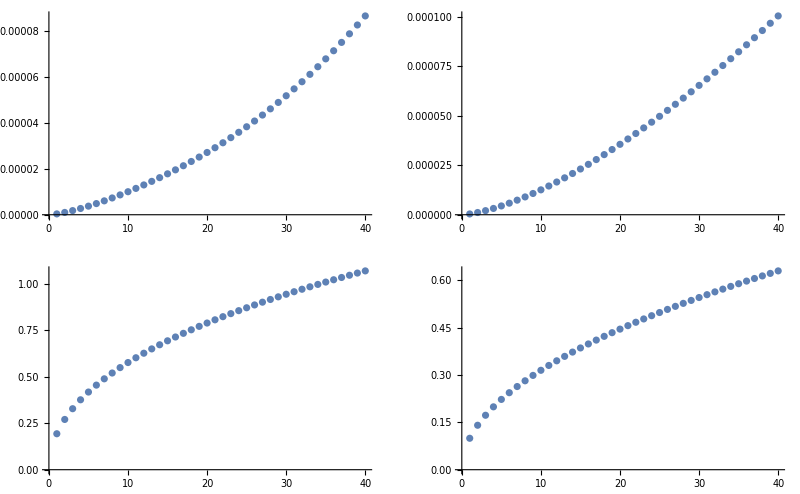

```mathematica
(*Lorenz number is jeat flux over (charge transport*Temp) *)
GraphicsGrid[{{ListPlot[heatAsymm1],ListPlot[heatsymm]},{ListPlot[chargeAsymm1],ListPlot[chargesymm]}},ImageSize->800]
```

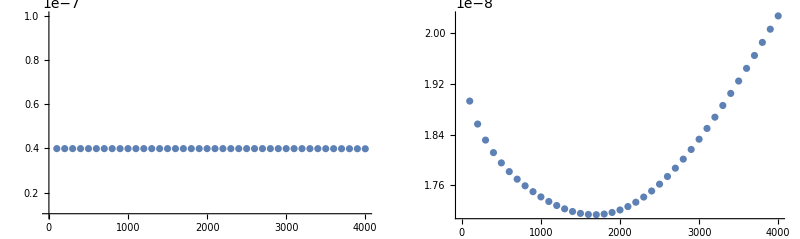

```mathematica
GraphicsGrid[{{ListPlot[Transpose@{temmps,heatsymm/(chargesymm*temmps)},PlotRange->{{0,4000},{10^-8,10^-7}}],ListPlot[Transpose@{temmps,heatAsymm1/(chargeAsymm1*temmps)}]}},ImageSize->800]
```

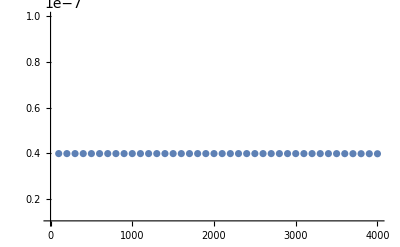

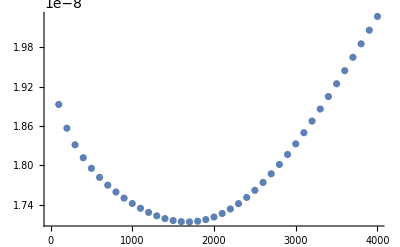

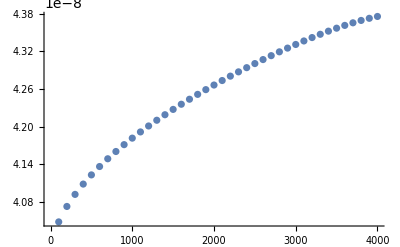

```mathematica
ListPlot[Transpose@{temmps,heatsymm/(chargesymm*temmps)},PlotRange->{{0,4000},{10^-8,10^-7}}]
ListPlot[Transpose@{temmps,heatAsymm1/(chargeAsymm1*temmps)}]
ListPlot[Transpose@{temmps,heatAsymm2/(chargeAsymm2*temmps)}]
```